## SOLVING THE TIME-DEPENDENT SCHRÖDINGER EQUATION WITH ABSORBING BOUNDARY CONDITIONS AND SOURCE TERMS IN MATHEMATICA 6.0 F. L. Dubeibe International Journal of Modern Physics C Vol. 21, No. 11 (2010) 1391

## Method with ABC

Define dimension N

```mathematica
n=1000;
```

Parameters

```mathematica
xmin = -20;      (*left border of the domain*)
xmax = 20-dx;      (* right border of the domain, the shift is for the size of the vector*)
dt=0.00192; (* time step *)
x0=0; (*initial position*)
dx = 2Abs[xmin]/n          (* space step changes with the size of the matrix N*)
```

1/25

Define α

```mathematica
α=0.3 ⅈ;
```

Define ABC coeficients

```mathematica
Subscript[α, 2]=25;
Subscript[α, 1]=24;
```

```mathematica
Subscript[g, 2]=(Subscript[α, 2] √(2 Subscript[α, 1])-Subscript[α, 1] √(2 Subscript[α, 2]))/(Subscript[α, 2]-Subscript[α, 1])//N
```

3.49945

```mathematica
Subscript[g, 1]=(√(2 Subscript[α, 2])-√(2 Subscript[α, 1]))/(Subscript[α, 2]-Subscript[α, 1])//N
```

0.142865

```mathematica
AB[1]=ⅈ/(2 dt);
```

```mathematica
AB[2]=ⅈ/(2 dt);
```

```mathematica
AB[3]=ⅈ/(2 dt)+ⅈ/(Subscript[g, 1] dx)-Subscript[g, 2]/(2 Subscript[g, 1]);
```

```mathematica
AB[4]=ⅈ/(2 dt)-ⅈ/(Subscript[g, 1] dx)-Subscript[g, 2]/(2 Subscript[g, 1]);
```

## Define Potential

```mathematica
potential[x_] :=Piecewise[{{500,x<-10},{500,10<=x<11}, {0,x>11} }]
```

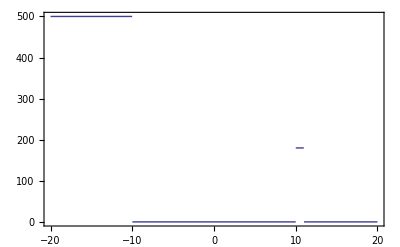

```mathematica
POT=Plot[potential[x],{x,-20,20}, Axes->False,Frame->True]
```

```mathematica
Do[V[i]=potential[i*dx+xmin],{i,0,n-1}]
```

```mathematica
V[n]=V[n-1];
```

```mathematica
Do[β[i]=ⅈ (dt/2)(1/(dx)^2+V[i])//Chop//N//Simplify,{i,0,n}];
```

```mathematica
a[1]=AB[1];
```

```mathematica
Do[a[i]=(1+β[i]),{i,2,n-1}];
```

```mathematica
a[n]=AB[2];
```

```mathematica
γ[1]=AB[3];
```

```mathematica
Do[γ[i]=(1-β[i]),{i,2,n-1}]
```

```mathematica
γ[n]=AB[4];
```

```mathematica
θ[0]=1;
```

```mathematica
θ[1]=AB[1];
```

```mathematica
θ[2]=a[2]AB[1]+α AB[2];
```

```mathematica
Do[θ[i]=(a[i]θ[i-1]-α^2 θ[i-2]),{i,3,n-1}]
```

```mathematica
θ[n]=(AB[2]θ[n-1]+α AB[1] θ[n-2])//Simplify;
```

```mathematica
Table[θ[i],{i,0,n}];
```

```mathematica
ϕ[n+1]=1;
```

```mathematica
ϕ[n]=AB[2];
```

```mathematica
ϕ[n-1]=a[n-1]AB[2]+AB[1]α;
```

```mathematica
Do[ϕ[i]=(a[i]ϕ[i+1]-α^2 ϕ[i+2]),{i,n-2,2,-1}]
```

```mathematica
ϕ[1]=AB[1]ϕ[2]-+α AB[2]ϕ[3];
```

```mathematica
Table[ϕ[i],{i,n+1,1,-1}];
```

```mathematica
t[1,1]=(ϕ [2])/θ[n];
```

```mathematica
Do[t[1,j]=((-1)^(1+j)AB[2](-α)^Abs[j-2] ϕ [j+1])/θ[n],{j,2,n}]
```

```mathematica
Do[If[i≤ j,t[i,j]=((-1)^(i+j)(-α)^Abs[j-i] θ[i-1]ϕ [j+1])/θ[n]],{i,2,n},{j,2,n}]
```

```mathematica
Do[If[i> j,t[i,j]=((-1)^(i+j)(-α)^Abs[i-j] θ[j-1]ϕ [i+1])/θ[n]],{i,2,n-1},{j,1,n}]
```

```mathematica
Do[t[n,j]=((-1)^(n+j)AB[1](-α)^Abs[n-j-1] θ[j-1])/θ[n],{j,1,n-1}]
```

```mathematica
Table[t[i,j],{i,1,n},{j,1,n}]//Simplify;
```

## Evolution Matrix

```mathematica
Do[R[i,1]=AB[4] t[i,1]+α t[i,2]//Chop,{i,1,n}]//Chop//Simplify;
```

```mathematica
Do[R[i,2]=AB[3] t[i,1]+γ[2] t[i,2]+α t[i,3]//Chop,{i,1,n}]//Chop//Simplify;
```

```mathematica
Do[R[i,k]=α t[i,k-1]+γ[k] t[i,k]+α t[i,k+1]//Chop,{i,1,n},{k,3,n-2}]//Chop//Simplify;
```

```mathematica
Do[R[i,n-1]=α t[i,n-2]+γ[n-1] t[i,n-1]+AB[3]  t[i,n]//Chop,{i,1,n}]//Chop//Simplify;
```

```mathematica
Do[R[i,n]=α t[i,n-1]+AB[4] t[i,n]//Chop,{i,1,n}]//Chop//Simplify;
```

```mathematica
RESM=Table[R[i,k]//Chop,{i,1,n},{k,1,n}]//Simplify//Chop;
```

## Discretisation of the wave function

```mathematica
Clear[p0]
```

```mathematica
p0=20;(*initial momentum*)
```

```mathematica
psi[0]=Table[Module[{x=x1-x0},(1./Pi)^(1/4) Exp[ⅈ*p0*x-x*x/2]],{x1,xmin,xmax,dx}];(*Initial wavepacket*)
```

## Evolution of the wave packet

```mathematica
tf=1000; (*Evolution time*)
pf=20;(*phi step*)
Do[psi[i+1]=RESM.psi[i],{i,0,tf}]//Simplify;(*It is the map*)
```

```mathematica
Do[psisquare[i]=Conjugate[psi[i]]*psi[i]//Chop,{i,0,tf+1,pf}]//FullSimplify
```

```mathematica
Evol=Table[ListPlot[psisquare[i],PlotRange->{-0.1,1},Joined->True,Filling->Axis,Frame->True,FrameTicks->{{{0,0.5,1},None},{{{0.0,0.0+xmin},{n/4,(0.0+xmin)/2},{n/2,0},{3n/4,(xmax+dx)/2},{n,xmax+dx}},None}}],{i,0,tf+1,pf}];
```

```mathematica
ListAnimate[Evol]
```

v